# How to get zero G_eq

## system size does not matter

```mathematica
ns={64,128,256,512,1024,2048,4096};
```

```mathematica
data=Table[Import["/home/chengling/Research/Project/Cell/glassyDynamics/systemSizeEffectGeq/simpleShearDerivatives_N"<>ToString[n]<>"_p3.8250_T0.06300000_mu1.0000_idx10.nc","Data"],{n,{64,128,256,512,1024,2048,4096}}];
```

```mathematica
Table[Variance[Flatten[Normal[data[[n,2]]]]]/0.063/Mean[Flatten[Normal[data[[n,1]]]]],{n,7}]
```

{0.774975,0.724182,0.766135,0.731947,0.756313,0.761734,0.756175}

```mathematica
Table[Mean[Flatten[Normal[data[[n,1]]]]/ns[[n]]],{n,7}]
```

{0.660517,0.657659,0.659897,0.661124,0.660467,0.661396,0.662043}

```mathematica
Table[Variance[Flatten[Normal[data[[n,2]]]]]/0.063/ns[[n]],{n,7}]
```

{0.511884,0.476265,0.50557,0.483908,0.49952,0.503808,0.50062}

```mathematica
Table[Mean[Flatten[Normal[data[[n,2]]]]]/0.063/ns[[n]],{n,7}]
```

{0.00070921,0.00831372,-0.00608413,-0.00403024,-0.00656261,-0.00143271,-0.00121531}

```mathematica
data[[7]]
```

<|/d2Edgammadgamma→NumericArray[…],/sigma→NumericArray[…]|>

```mathematica
data=Table[Import["/home/chengling/Research/Project/Cell/glassyDynamics/systemSizeEffectGeq/simpleShearDerivatives_N"<>ToString[n]<>"_p3.8250_T0.06300000_mu0.1000_idx10.nc","Data"],{n,{64,128,256,512,1024,2048,4096}}];
```

```mathematica
Table[Variance[Flatten[Normal[data[[n,2]]]]]/0.063/Mean[Flatten[Normal[data[[n,1]]]]],{n,7}]
```

{0.758641,0.719867,0.695934,0.718057,0.70349,0.694865,0.702894}

```mathematica
Table[Mean[Flatten[Normal[data[[n,1]]]]/ns[[n]]],{n,7}]
```

{0.651351,0.654363,0.665355,0.659191,0.659842,0.661598,0.66219}

```mathematica
Table[Mean[Flatten[Normal[data[[n,1]]]]],{n,7}]
```

{41.6865,83.7585,170.331,337.506,675.678,1354.95,2712.33}

```mathematica
data=Table[Import["/home/chengling/Research/Project/Cell/glassyDynamics/systemSizeEffectGeq/simpleShearDerivatives_N"<>ToString[n]<>"_p3.8250_T0.06300000_mu10.0000_idx10.nc","Data"],{n,{64,128,256,512,1024,2048,4096}}];
```

```mathematica
Table[Variance[Flatten[Normal[data[[n,2]]]]]/0.063/Mean[Flatten[Normal[data[[n,1]]]]],{n,7}]
```

{1.20527,1.29039,1.31645,1.31251,1.36981,1.26129,1.28824}

```mathematica
Table[Mean[Flatten[Normal[data[[n,1]]]]/ns[[n]]],{n,7}]
```

{0.674466,0.670046,0.670344,0.670516,0.672162,0.670327,0.670982}

```mathematica
Table[Variance[Flatten[Normal[data[[n,2]]]]]/0.063/ns[[n]],{n,7}]
```

{0.81291,0.864618,0.882477,0.880058,0.920732,0.845477,0.864384}

## Inverse coefficient of BD matters

```mathematica
μs={0.1,1.,2.,3.,4.,5.,6.,7.,8.,9.,10.,11.,12.,13.};
dts={0.001 ,0.005, 0.01, 0.02, 0.04, 0.06, 0.08, 0.1};
Ts={0.063,0.01};
```

```mathematica
differentmu=Table[Table[Import[dataNameStringNumber[{"/home/chengling/Research/Project/Cell/glassyDynamics/systematicGeq/simpleShearDerivatives1st2nd_bd_N1024_p3.8250_T","_mu","_idx10.nc"},{Ts[[T]],μs[[mu]]},{8,4}],"Data"],{mu,Length[μs]}],{T,Length[Ts]}];
```

```mathematica
nvt=Table[Table[Import[dataNameStringNumber[{"/home/chengling/Research/Project/Cell/glassyDynamics/systematicGeq/simpleShearDerivatives1st2nd_nvt_N1024_p3.8250_T","_dt","_idx10.nc"},{Ts[[T]],dts[[dt]]},{8,4}],"Data"],{dt,Length[dts]}],{T,1}];
```

```mathematica
differentmuSigmai=Table[Table[Import[dataNameStringNumber[{"/home/chengling/Research/Project/Cell/glassyDynamics/systematicGeq/simpleShearDerivativesPerCell_bd_N1024_p3.8250_T","_mu","_idx10.nc"},{Ts[[T]],μs[[mu]]},{8,4}],"Data"],{mu,Length[μs]}],{T,Length[Ts]}];
```

```mathematica
nvtSigmai=Table[Table[Import[dataNameStringNumber[{"/home/chengling/Research/Project/Cell/glassyDynamics/systematicGeq/simpleShearDerivativesPerCell_nvt_N1024_p3.8250_T","_dt","_idx10.nc"},{Ts[[T]],dts[[dt]]},{8,4}],"Data"],{dt,Length[dts]}],{T,1}];
```

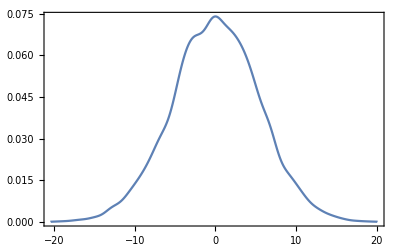

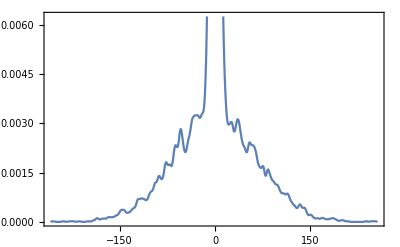

```mathematica
SmoothHistogram[Normal[nvt[[1,5,1]]]]
SmoothHistogram[Normal[nvt[[1,6,1]]]]
```

#### ratio of G_2/G_1

```mathematica
rationvt=Table[Table[Variance[Flatten[Normal[nvt[[T,n,1]]]]]/Ts[[T]]/Mean[Flatten[Normal[nvt[[T,n,2]]]]],{n,Length[dts]}],{T,1}]
```

{{0.699833,0.721511,0.698437,0.690667,0.683869,21.5034,0.688848,26.1196}}

```mathematica
ratio=Table[Table[Variance[Flatten[Normal[differentmu[[T,n,1]]]]]/Ts[[T]]/Mean[Flatten[Normal[differentmu[[T,n,2]]]]],{n,Length[μs]}],{T,Length[Ts]}]
```

{{0.700812,0.731938,0.774754,0.80926,0.850907,0.888897,0.948393,1.01511,1.10456,1.1966,1.30837,1.48044,1.62705,1.91857},{0.878895,0.908734,0.948111,0.990898,1.01326,1.06615,1.1336,1.15235,1.25001,1.33715,1.44301,1.6134,1.80302,2.1045}}

```mathematica
g2=Table[Table[Variance[Flatten[Normal[differentmu[[T,n,1]]]]]/1024/Ts[[T]],{n,Length[μs]}],{T,Length[Ts]}]
```

{{0.463986,0.483579,0.511603,0.534262,0.560715,0.586175,0.625544,0.671059,0.732333,0.797022,0.877848,1.00457,1.12222,1.36303},{0.252768,0.260039,0.271353,0.283208,0.288895,0.303471,0.322053,0.326708,0.353102,0.376244,0.404526,0.449665,0.499227,0.577521}}

```mathematica
g2nvt=Table[Table[Variance[Flatten[Normal[nvt[[T,n,1]]]]]/1024/Ts[[T]],{n,Length[dts]}],{T,1}]
```

{{0.463067,0.477631,0.462147,0.456752,0.451665,36.1926,0.451953,66.4706}}

```mathematica
g1=Table[Table[Mean[Flatten[Normal[differentmu[[T,n,2]]]]]/1024,{n,Length[μs]}],{T,Length[Ts]}]
```

{{0.662069,0.660684,0.660343,0.660186,0.658961,0.659441,0.659583,0.661073,0.663011,0.666075,0.670948,0.678558,0.689728,0.710437},{0.287598,0.286156,0.286204,0.28581,0.285115,0.284643,0.284098,0.283514,0.282478,0.281378,0.280335,0.278706,0.276884,0.274422}}

```mathematica
g1nvt=Table[Table[Mean[Flatten[Normal[nvt[[T,n,2]]]]]/1024,{n,Length[dts]}],{T,1}]
```

{{0.661682,0.661987,0.661688,0.66132,0.660457,1.68311,0.656099,2.54486}}

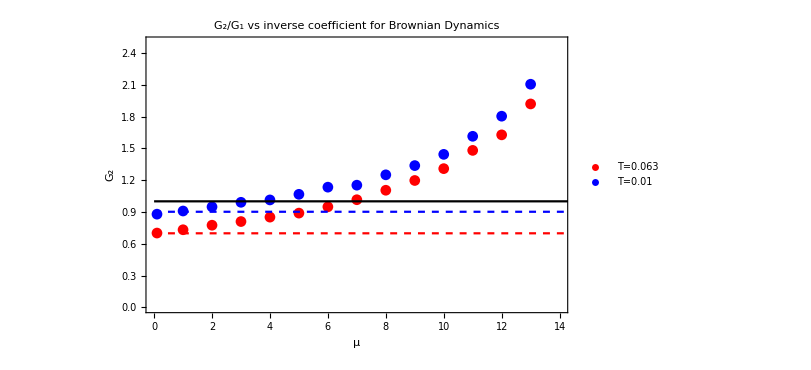

```mathematica
ratioPlots=Show[ListPlot[Table[Table[{μs[[mu]],ratio[[T,mu]]},{mu,Length[μs]}],{T,Length[Ts]}],FrameLabel->{"μ","G_2"},ImageSize->600,PlotStyle->{Red,Blue},PlotLegends->{"T=0.063","T=0.01"},PlotLabel->"G_2/G_1 vs inverse coefficient for Brownian Dynamics",PlotRange->{{0,14},{0,2.5}}],Plot[rationvt[[1]],{x,0,15},PlotStyle->{Dashed,Thick,Red}],Plot[rationvt[[2]],{x,0,15},PlotStyle->{Dashed,Thick,Blue},PlotLegends->"Dashes line: nvt"],Plot[1,{x,0,15},PlotStyle->{Black},PlotLegends->"Black solid line: G_2/G_1=1"]]
```

```mathematica
Export["/home/chengling/Research/updates/04252024/ratio.jpeg",ratioPlots,ImageResolution->600]
```

/home/chengling/Research/updates/04252024/ratio.jpeg

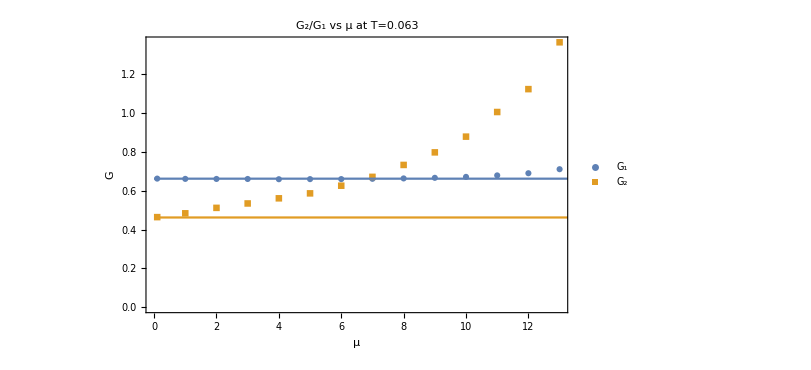
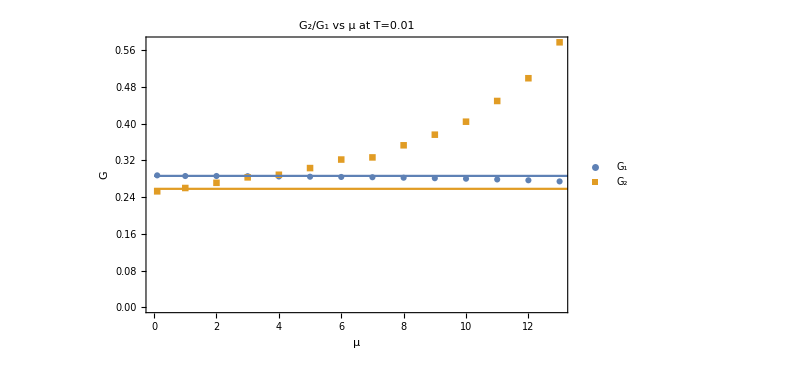

```mathematica
gtermsPlots=Table[Show[ListPlot[{Table[{μs[[mu]],g1[[T,mu]]},{mu,Length[μs]}],Table[{μs[[mu]],g2[[T,mu]]},{mu,Length[μs]}]},FrameLabel->{"μ","G"},ImageSize->600,PlotMarkers->Automatic,PlotLegends->{"G_1","G_2"},PlotLabel->"G_2/G_1 vs μ at T="<>ToString[Ts[[T]]]],Plot[{g1nvt[[T]],g2nvt[[T]]},{x,0,15},PlotStyle->Automatic,PlotLegends->"Solid line: nvt"]],{T,Length[Ts]}]
```

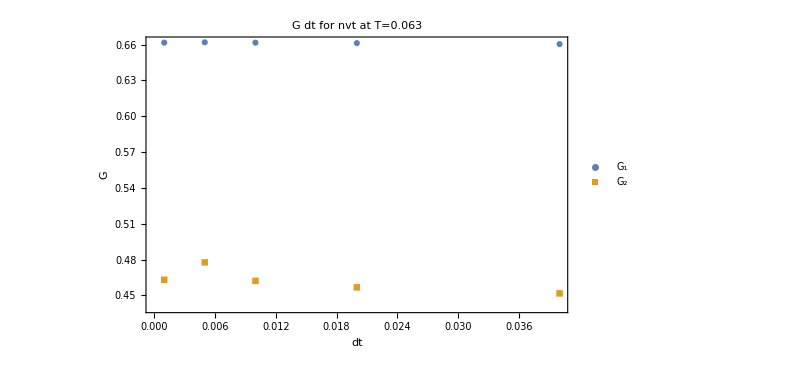

```mathematica
gtermsPlotsNVT=Table[Show[ListPlot[{Table[{dts[[mu]],g1nvt[[T,mu]]},{mu,5}],Table[{dts[[mu]],g2nvt[[T,mu]]},{mu,5}]},FrameLabel->{"dt","G"},ImageSize->600,PlotMarkers->Automatic,PlotLegends->{"G_1","G_2"},PlotLabel->"G dt for nvt at T="<>ToString[Ts[[T]]]]],{T,1}]
```

```mathematica
Table[Export["/home/chengling/Research/updates/04252024/gterms"<>ToString[Ts[[T]]]<>".jpeg",gtermsPlots[[T]],ImageResolution->600],{T,Length[Ts]}]
```

{/home/chengling/Research/updates/04252024/gterms0.063.jpeg,/home/chengling/Research/updates/04252024/gterms0.01.jpeg}

```mathematica
Table[Export["/home/chengling/Research/updates/04252024/gtermsNVT"<>ToString[Ts[[T]]]<>".jpeg",gtermsPlotsNVT[[T]],ImageResolution->600],{T,1}]
```

{/home/chengling/Research/updates/04252024/gtermsNVT0.063.jpeg}

### distribution

```mathematica
SetOptions[SmoothHistogram,DMSopts];
```

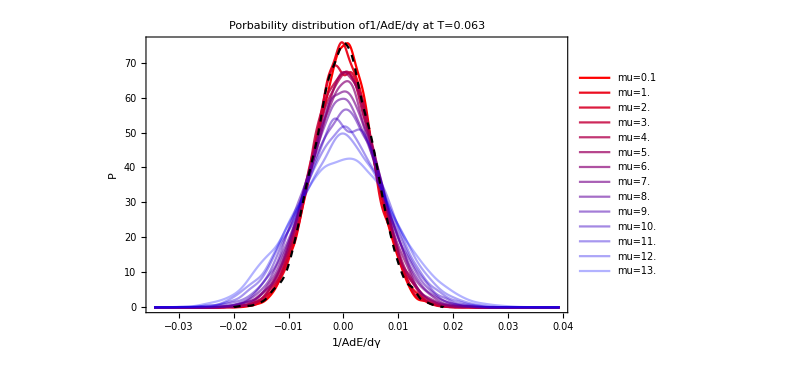
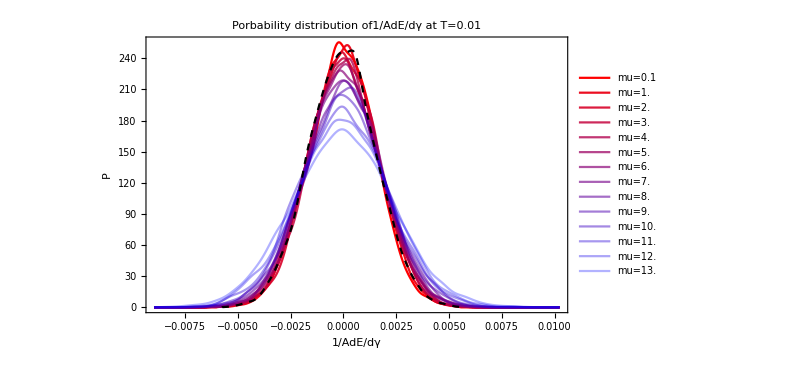

```mathematica
distributions=Table[Show[SmoothHistogram[Table[Flatten[Normal[differentmu[[T,n,1]]]/1024],{n,Length[μs]}],PlotStyle->redBluePlotConfig[Length[μs]],PlotLegends->Table["mu="<>ToString[μs[[n]]],{n,Length[μs]}],ImageSize->600,PlotLabel->"Porbability distribution of1/AdE/dγ at T="<>ToString[Ts[[T]]],FrameLabel->{"1/AdE/dγ","P"}],SmoothHistogram[Flatten[Normal[nvt[[T,1]]]/1024],PlotStyle->{Dashed,Thick,Black},PlotLegends->"Dashed line: nvt"]],{T,Length[Ts]}];
Column[distributions]
```

```mathematica
Table[Export["/home/chengling/Research/updates/04252024/stressPD"<>ToString[Ts[[T]]]<>".jpeg",distributions[[T]],ImageResolution->600],{T,Length[Ts]}]
```

{/home/chengling/Research/updates/04252024/stressPD0.063.jpeg,/home/chengling/Research/updates/04252024/stressPD0.01.jpeg}

### SAC

```mathematica
Croverlapdifferentmu=Table[Table[Import[dataNameStringNumber[{"/home/chengling/Research/Project/Cell/glassyDynamics/systematicGeq/CRoverlapTime_bd_N1024_p3.8250_T","_mu","_idx10.nc"},{Ts[[T]],μs[[mu]]},{8,4}],"Data"],{mu,Length[μs]}],{T,2}];
```

```mathematica
Croverlapnvt=Table[Import[dataNameStringNumber[{"/home/chengling/Research/Project/Cell/glassyDynamics/systematicGeq/CRoverlapTime_nvt_N1024_p3.8250_T","_mu1.0000_idx10.nc"},{Ts[[T]]},{8,4}],"Data"],{T,2}];
```

```mathematica
Croverlapdifferentmu[[1,1]]
```

<|/firstValue→NumericArray[…],/secondValue→NumericArray[…]|>

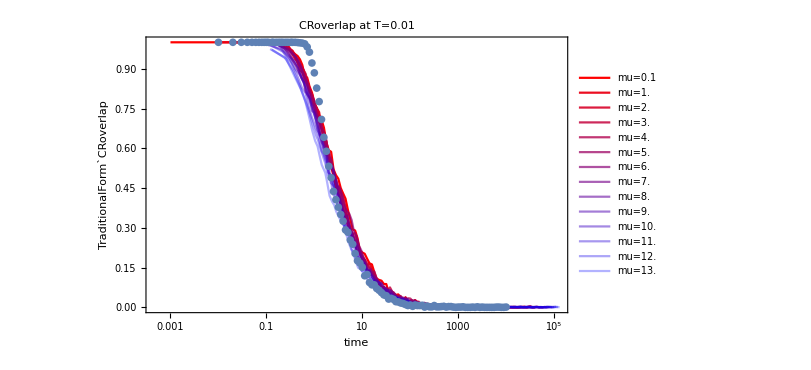
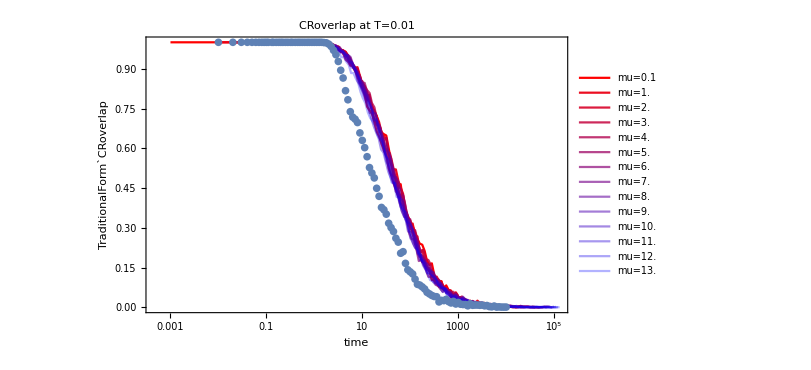

```mathematica
CRoverlapPlots=Table[Show[ListLogLinearPlot[Table[Table[{(Croverlapdifferentmu[[T,mu,2,i]]-Croverlapdifferentmu[[T,mu,2,1]])*μs[[mu]],Croverlapdifferentmu[[T,mu,1,i]]},{i,Length[Croverlapdifferentmu[[T,mu,1]]]}],{mu,Length[μs]}],FrameLabel->{"time","TraditionalForm`CRoverlap"},ImageSize->600,PlotStyle->redBluePlotConfig[Length[μs]],Joined->True,PlotLegends->Table["mu="<>ToString[μs[[n]]],{n,Length[μs]}],PlotLabel->"CRoverlap at T="<>ToString[Ts[[2]]]],ListLogLinearPlot[Table[{Croverlapnvt[[T,2,i]]-Croverlapnvt[[T,2,1]],Croverlapnvt[[T,1,i]]},{i,Length[Croverlapnvt[[T,1]]]}],PlotStyle->Automatic,PlotLegends->"Blue dots: nvt"]],{T,Length[Ts]}];
Column[CRoverlapPlots]
```

```mathematica
Table[Export["/home/chengling/Research/updates/04252024/CRoverlapScaled"<>ToString[Ts[[T]]]<>".jpeg",CRoverlapPlots[[T]],ImageResolution->600],{T,Length[Ts]}]
```

{/home/chengling/Research/updates/04252024/CRoverlapScaled0.063.jpeg,/home/chengling/Research/updates/04252024/CRoverlapScaled0.01.jpeg}

### SAC

```mathematica
SACdifferentmu=Table[Table[Import[dataNameStringNumber[{"/home/chengling/Research/Project/Cell/glassyDynamics/systematicGeq/SACtime_bd_N1024_p3.8250_T","_mu","_idx10.nc"},{Ts[[T]],μs[[mu]]},{8,4}],"Data"],{mu,Length[μs]}],{T,2,2}];
```

```mathematica
SACnvt=Table[Import[dataNameStringNumber[{"/home/chengling/Research/Project/Cell/glassyDynamics/systematicGeq/CRoverlapTime_nvt_N1024_p3.8250_T","_mu1.0000_idx10.nc"},{Ts[[T]]},{8,4}],"Data"],{T,2,2}];
```

```mathematica
Croverlapdifferentmu[[1,1]]
```

<|/firstValue→NumericArray[…],/secondValue→NumericArray[…]|>

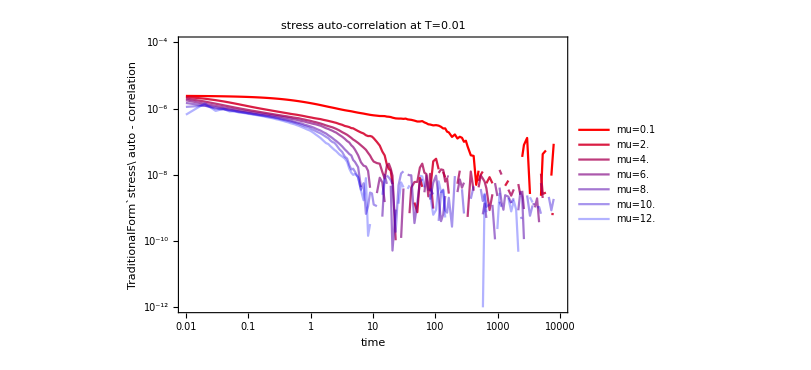
Column[-Graphics-]

```mathematica
SACPlots=Show[ListLogLogPlot[Table[Table[{SACdifferentmu[[1,mu,2,i]]-SACdifferentmu[[1,mu,2,1]],SACdifferentmu[[1,mu,1,i]]},{i,Length[SACdifferentmu[[1,mu,1]]]}],{mu,1,Length[μs],2}],FrameLabel->{"time","TraditionalForm`stress\ auto - correlation"},ImageSize->600,PlotStyle->redBluePlotConfig[Length[μs]/2],Joined->True,PlotRange->{{0.01,10000},{10^-4,10^-12}},PlotLegends->Table["mu="<>ToString[μs[[mu]]],{mu,1,Length[μs],2}],PlotLabel->"stress auto-correlation at T="<>ToString[Ts[[2]]]],ListLogLinearPlot[Table[{SACnvt[[1,2,i]]-SACnvt[[1,2,1]],SACnvt[[1,1,i]]},{i,Length[SACnvt[[1,1]]]}],PlotStyle->Automatic,PlotLegends->"Blue dots: nvt"]];
Column[SACPlots]
```

```mathematica
Export["/home/chengling/Research/updates/04252024/SAC.jpeg",SACPlots,ImageResolution->600]
```

/home/chengling/Research/updates/04252024/SAC.jpeg

### The variance in particle level

```mathematica
overallVar=Table[Table[Variance[Flatten[Join[Table[Normal[differentmuSigmai[[T,n,2,i]]],{i,Length[differentmuSigmai[[T,n,2]]]}]]]],{n,Length[μs]}]/0.063,{T,Length[Ts]}]
```

{{0.326985,0.336554,0.359515,0.37814,0.39537,0.422491,0.451904,0.471632,0.525266,0.577264,0.642778,0.712566,0.822528,0.984142},{0.0302734,0.0306281,0.0320587,0.0338923,0.0349198,0.0373111,0.0393751,0.0406972,0.0438833,0.0472793,0.050322,0.0555353,0.0643141,0.0724152}}

```mathematica
overallVar/g2/0.063
```

{{11.1862,11.047,11.1543,11.2346,11.1923,11.4406,11.4669,11.1558,11.3849,11.4964,11.6225,11.2592,11.6341,11.4607},{1.90107,1.86956,1.8753,1.89957,1.91863,1.95155,1.94068,1.97726,1.97269,1.99462,1.97456,1.96038,2.04488,1.99032}}

```mathematica
singleconfiVar=Table[Table[Mean[Table[Variance[Normal[differentmuSigmai[[T,n,2,i]]]],{i,Length[differentmuSigmai[[T,n,2]]]}]],{n,Length[μs]}],{T,Length[Ts]}]
```

{{0.0205966,0.0211976,0.0226423,0.0238107,0.0248955,0.0266082,0.0284641,0.0297061,0.0330856,0.0363537,0.0404781,0.044877,0.0518042,0.0619828},{0.00190635,0.00192823,0.00201945,0.00213523,0.00219915,0.00235024,0.0024805,0.00256317,0.00276368,0.00297771,0.00316892,0.0034966,0.00405049,0.00456229}}

```mathematica
g2100conf=Table[Table[Variance[Table[Total[Normal[differentmuSigmai[[T,n,2,i]]]],{i,Length[differentmuSigmai[[T,n,2]]]}]],{n,Length[μs]}]/1024/0.063,{T,Length[Ts]}]
```

{{0.383922,0.423227,0.477049,0.577866,0.606174,0.56545,0.546699,0.581198,0.625774,0.805486,0.919749,0.953506,1.06947,1.28158},{0.0446476,0.0526487,0.0361103,0.0336711,0.0479814,0.0431804,0.0415164,0.0530011,0.0598122,0.0617457,0.0726247,0.0903181,0.0855947,0.0703497}}

```mathematica
g2100conf/g2
```

{{0.827444,0.875196,0.932459,1.08162,1.08107,0.964643,0.873957,0.86609,0.854495,1.01062,1.04773,0.949173,0.952999,0.940248},{0.176635,0.202464,0.133075,0.118892,0.166086,0.142288,0.128912,0.162228,0.169391,0.164111,0.17953,0.200856,0.171454,0.121813}}

```mathematica
singleconfiVar/overallVar
```

{{0.0629894,0.0629843,0.0629801,0.0629678,0.0629675,0.0629794,0.0629872,0.0629858,0.0629883,0.0629759,0.0629737,0.0629794,0.0629817,0.0629816},{0.062971,0.0629562,0.0629923,0.0630004,0.0629772,0.0629904,0.0629967,0.0629816,0.0629779,0.0629813,0.062973,0.0629618,0.0629798,0.0630017}}

```mathematica
singleconfiVar/g2
```

{{0.0443905,0.0438348,0.0442575,0.0445674,0.0443995,0.0453929,0.045503,0.0442675,0.0451784,0.0456119,0.0461107,0.044673,0.0461623,0.0454744},{0.00754188,0.00741513,0.00744215,0.00753943,0.0076123,0.00774453,0.00770216,0.00784546,0.00782686,0.00791431,0.00783366,0.00777603,0.00811352,0.00789978}}

### nvt

```mathematica
Import["/home/chengling/Research/Project/Cell/glassyDynamics/systematicGeq/simpleShearDerivatives1st2nd_bd_N1024_p3.8250_T0.06300000_mu0.1000_idx10.nc","Data"]
```

<|/firstValue→NumericArray[…],/secondValue→NumericArray[…]|>

```mathematica
nvt=Import["/home/chengling/Research/Project/Cell/glassyDynamics/systematicGeq/simpleShearDerivatives1st2nd_nvt_N1024_p3.8250_T0.06300000_mu1.0000_idx10.nc","Data"];
```

```mathematica
Variance[Flatten[Normal[nvt[[1]]]]]/0.063/Mean[Flatten[Normal[nvt[[2]]]]]
```

0.698437